```mathematica
line[z_]:=ListLinePlot[Table[{x,z},{x,Range[1,20,0.01]}],PlotStyle->Gray]
```

```mathematica
line1[z_]:=ListLinePlot[Table[{x,z},{x,Range[0,21,0.01]}],PlotStyle->Blue]
```

```mathematica
p1[z_]:=ListLinePlot[Table[{z,y},{y,Range[0,21,1]}],PlotStyle->Blue]
```

```mathematica
p[z_]:=ListLinePlot[Table[{x,y},{x,Range[1,20,1]},{y,Range[1,20,1]}][[z]],PlotStyle->Gray]
```

```mathematica
lead=ParallelTable[ToExpression[Import["/home/shardulmukim/PhD/fwi/sq_lattice/20sq/lead_new/L_"<>ToString[ω]<>".dat"]],{ω,Range[0,4,0.01]}]
```

{1}
 |  |  |  |

```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->-t]
```

```mathematica
T[t_,m_]:=T[t,m]=t*IdentityMatrix[m]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_,m_]:=LEFT[ω,δ,t,ϵ,m]=lead[[ω*100+1]]
```

```mathematica
g[ω_,δ_,t_,ϵ_,m_]:= Inverse[β[ω,δ,t,ϵ,m]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-g[ω,δ,t,ϵ,m].T[t,m].LEFT[ω,δ,t,ϵ,m].T[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-g[ω,δ,t,ϵ,m].T[t,m].LEFT[ω,δ,t,ϵ,m].T[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-SL[ω,δ,t,ϵ,m].T[t,m].SR[ω,δ,t,ϵ,m].T[t,m]].SL[ω,δ,t,ϵ,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-SR[ω,δ,t,ϵ,m].T[t,m].SL[ω,δ,t,ϵ,m].T[t,m]].SR[ω,δ,t,ϵ,m]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,m_]:= IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,m_]:= IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,m_]:= SR[ω,δ,t,ϵ,m].T[t,m].IL[ω,δ,t,ϵ,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,m_]:= Abs[Tr[gdd[ω,δ,t,ϵ,m].T[t,m].grr[ω,δ,t,ϵ,m].T[t,m]-T[t,m].GNON[ω,δ,t,ϵ,m].T[t,m].GNON[ω,δ,t,ϵ,m]]]
```

```mathematica
pris=Table[{ω,Abs[tr[ω,0.0001,1,0,20]]},{ω,Range[0,4,0.01]}]
```

{{0.,20.},{0.01,20.},{0.02,19.9995},{0.03,19.},{0.04,19.},{0.05,19.},{0.06,19.},{0.07,19.},{0.08,19.},{0.09,18.0019},{0.1,18.},{0.11,18.},{0.12,18.},{0.13,18.},{0.14,18.},{0.15,18.},{0.16,18.},{0.17,18.},{0.18,18.},{0.19,18.},{0.2,17.0007},{0.21,17.},{0.22,17.},{0.23,17.},{0.24,17.},{0.25,17.},{0.26,17.},{0.27,17.},{0.28,17.},{0.29,17.},{0.3,17.},{0.31,17.},{0.32,17.},{0.33,17.},{0.34,17.},{0.35,16.0004},{0.36,16.},{0.37,16.},{0.38,16.},{0.39,16.},{0.4,16.},{0.41,16.},{0.42,16.},{0.43,16.},{0.44,16.},{0.45,16.},{0.46,16.},{0.47,16.},{0.48,16.},{0.49,16.},{0.5,16.},{0.51,16.},{0.52,16.},{0.53,15.9998},{0.54,15.0001},{0.55,15.},{0.56,15.},{0.57,15.},{0.58,15.},{0.59,15.},{0.6,15.},{0.61,15.},{0.62,15.},{0.63,15.},{0.64,15.},{0.65,15.},{0.66,15.},{0.67,15.},{0.68,15.},{0.69,15.},{0.7,15.},{0.71,15.},{0.72,15.},{0.73,15.},{0.74,15.},{0.75,14.9997},{0.76,14.0001},{0.77,14.},{0.78,14.},{0.79,14.},{0.8,14.},{0.81,14.},{0.82,14.},{0.83,14.},{0.84,14.},{0.85,14.},{0.86,14.},{0.87,14.},{0.88,14.},{0.89,14.},{0.9,14.},{0.91,14.},{0.92,14.},{0.93,14.},{0.94,14.},{0.95,14.},{0.96,14.},{0.97,14.},{0.98,14.},{0.99,14.},{1.,13.5},{1.01,13.},{1.02,13.},{1.03,13.},{1.04,13.},{1.05,13.},{1.06,13.},{1.07,13.},{1.08,13.},{1.09,13.},{1.1,13.},{1.11,13.},{1.12,13.},{1.13,13.},{1.14,13.},{1.15,13.},{1.16,13.},{1.17,13.},{1.18,13.},{1.19,13.},{1.2,13.},{1.21,13.},{1.22,13.},{1.23,13.},{1.24,13.},{1.25,13.},{1.26,13.},{1.27,12.0053},{1.28,12.},{1.29,12.},{1.3,12.},{1.31,12.},{1.32,12.},{1.33,12.},{1.34,12.},{1.35,12.},{1.36,12.},{1.37,12.},{1.38,12.},{1.39,12.},{1.4,12.},{1.41,12.},{1.42,12.},{1.43,12.},{1.44,12.},{1.45,12.},{1.46,12.},{1.47,12.},{1.48,12.},{1.49,12.},{1.5,12.},{1.51,12.},{1.52,12.},{1.53,12.},{1.54,12.},{1.55,11.9999},{1.56,11.0001},{1.57,11.},{1.58,11.},{1.59,11.},{1.6,11.},{1.61,11.},{1.62,11.},{1.63,11.},{1.64,11.},{1.65,11.},{1.66,11.},{1.67,11.},{1.68,11.},{1.69,11.},{1.7,11.},{1.71,11.},{1.72,11.},{1.73,11.},{1.74,11.},{1.75,11.},{1.76,11.},{1.77,11.},{1.78,11.},{1.79,11.},{1.8,11.},{1.81,11.},{1.82,11.},{1.83,11.},{1.84,11.},{1.85,10.9916},{1.86,10.},{1.87,10.},{1.88,10.},{1.89,10.},{1.9,10.},{1.91,10.},{1.92,10.},{1.93,10.},{1.94,10.},{1.95,10.},{1.96,10.},{1.97,10.},{1.98,10.},{1.99,10.},{2.,10.},{2.01,10.},{2.02,10.},{2.03,10.},{2.04,10.},{2.05,10.},{2.06,10.},{2.07,10.},{2.08,10.},{2.09,10.},{2.1,10.},{2.11,10.},{2.12,10.},{2.13,9.99999},{2.14,9.99997},{2.15,9.00836},{2.16,9.00002},{2.17,9.00001},{2.18,9.},{2.19,9.},{2.2,9.},{2.21,9.},{2.22,9.},{2.23,9.},{2.24,9.},{2.25,9.},{2.26,9.},{2.27,9.},{2.28,9.},{2.29,9.},{2.3,9.},{2.31,9.},{2.32,9.},{2.33,9.},{2.34,9.},{2.35,9.},{2.36,9.},{2.37,9.},{2.38,9.},{2.39,9.},{2.4,9.},{2.41,9.},{2.42,9.},{2.43,8.99999},{2.44,8.9999},{2.45,8.0001},{2.46,8.00001},{2.47,8.},{2.48,8.},{2.49,8.},{2.5,8.},{2.51,8.},{2.52,8.},{2.53,8.},{2.54,8.},{2.55,8.},{2.56,8.},{2.57,8.},{2.58,8.},{2.59,8.},{2.6,8.},{2.61,8.},{2.62,8.},{2.63,8.},{2.64,8.},{2.65,8.},{2.66,8.},{2.67,8.},{2.68,8.},{2.69,8.},{2.7,8.},{2.71,7.99999},{2.72,7.99998},{2.73,7.99471},{2.74,7.00003},{2.75,7.00001},{2.76,7.},{2.77,7.},{2.78,7.},{2.79,7.},{2.8,7.},{2.81,7.},{2.82,7.},{2.83,7.},{2.84,7.},{2.85,7.},{2.86,7.},{2.87,7.},{2.88,7.},{2.89,7.},{2.9,7.},{2.91,7.},{2.92,7.},{2.93,7.},{2.94,7.},{2.95,7.},{2.96,7.},{2.97,7.},{2.98,6.99999},{2.99,6.99997},{3.,6.49999},{3.01,6.00002},{3.02,6.00001},{3.03,6.},{3.04,6.},{3.05,6.},{3.06,6.},{3.07,6.},{3.08,6.},{3.09,6.},{3.1,6.},{3.11,6.},{3.12,6.},{3.13,6.},{3.14,6.},{3.15,6.},{3.16,6.},{3.17,6.},{3.18,6.},{3.19,6.},{3.2,6.},{3.21,6.},{3.22,6.},{3.23,5.99999},{3.24,5.99995},{3.25,5.00027},{3.26,5.00001},{3.27,5.},{3.28,5.},{3.29,5.},{3.3,5.},{3.31,5.},{3.32,5.},{3.33,5.},{3.34,5.},{3.35,5.},{3.36,5.},{3.37,5.},{3.38,5.},{3.39,5.},{3.4,5.},{3.41,5.},{3.42,5.},{3.43,5.},{3.44,5.},{3.45,4.99999},{3.46,4.99993},{3.47,4.00016},{3.48,4.00001},{3.49,4.},{3.5,4.},{3.51,4.},{3.52,4.},{3.53,4.},{3.54,4.},{3.55,4.},{3.56,4.},{3.57,4.},{3.58,4.},{3.59,4.},{3.6,4.},{3.61,4.},{3.62,4.},{3.63,3.99999},{3.64,3.99998},{3.65,3.99959},{3.66,3.00004},{3.67,3.00001},{3.68,3.},{3.69,3.},{3.7,3.},{3.71,3.},{3.72,3.},{3.73,3.},{3.74,3.},{3.75,3.},{3.76,3.},{3.77,3.},{3.78,2.99999},{3.79,2.99998},{3.8,2.99933},{3.81,2.00004},{3.82,2.00001},{3.83,2.},{3.84,2.},{3.85,2.},{3.86,2.},{3.87,2.},{3.88,2.},{3.89,1.99999},{3.9,1.99998},{3.91,1.9981},{3.92,1.00003},{3.93,1.00001},{3.94,1.},{3.95,0.999998},{3.96,0.999993},{3.97,0.999958},{3.98,0.000456674},{3.99,0.0000168049},{4.,5.34708×10^-6}}

```mathematica
im[ω_,μ_,λ_,q_,ϵ1_,m_]:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ,μ},{λ,λ},{q,q}}->ω+ⅈ*0.0001-ϵ1]]]
```

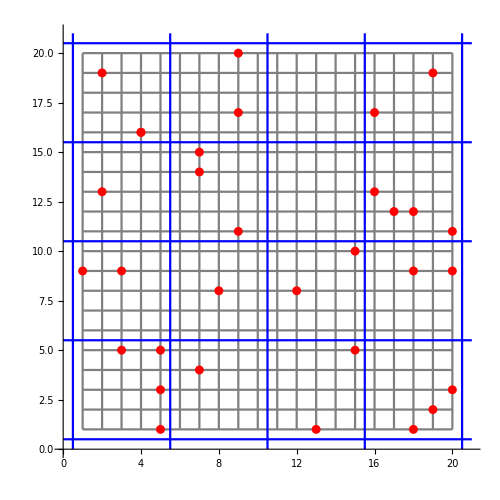

```mathematica
Show[Show[Table[p[z],{z,20}],Table[line[z],{z,20}],ListPlot[Table[{RandomInteger[{1,20}],RandomInteger[{1,20}]},32],PlotStyle->Red],(*ListPlot[{{3,12},{11,17},{20,8},{8,5}},PlotStyle->Black],*)PlotRange->All],Show[line1[0.5],line1[5.5],line1[10.5],line1[15.5],line1[20.5],PlotRange->All],Show[p1[0.5],p1[5.5],p1[10.5],p1[15.5],p1[20.5],PlotRange->All],ImageSize->{500,500},AspectRatio->Full]
```

```mathematica
Clear[im]
```

```mathematica
{im[ω,μ,λ,q,ϵ1,20],im[ω,μ,λ,q,ϵ1,20],im[ω,μ,λ,q,ϵ1,20],im[ω,μ,λ,q,ϵ1,20],im[ω,μ,λ,q,ϵ1,20],im[ω,μ,λ,q,ϵ1,20],im[ω,μ,λ,q,ϵ1,20],im[ω,μ,λ,q,ϵ1,20],im[ω,μ,λ,q,ϵ1,20],im[ω,μ,λ,q,ϵ1,20],im[ω,μ,λ,q,ϵ1,20],im[ω,μ,λ,q,ϵ1,20],im[ω,μ,λ,q,ϵ1,20],im[ω,μ,λ,q,ϵ1,20],im[ω,μ,λ,q,ϵ1,20],im[ω,μ,λ,q,ϵ1,20],im[ω,μ,λ,q,ϵ1,20],im[ω,μ,λ,q,ϵ1,20],im[ω,μ,λ,q,ϵ1,20],im[ω,μ,λ,q,ϵ1,20]}
```

```mathematica
im4[ω_,μ_,λ_,q_,r_,ϵ1_,m_]:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ,μ},{λ,λ},{q,q},{r,r}}->ω+ⅈ*0.0001-ϵ1]]]
```

```mathematica
im5[ω_,μ_,λ_,q_,r_,ψ_,ϵ1_,m_]:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ,μ},{λ,λ},{q,q},{r,r},{ψ,ψ}}->ω+ⅈ*0.0001-ϵ1]]]
```

```mathematica
imp[ω_,m_,ϵ1_]:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{1,1},{2,2},{3,3}}->ω+ⅈ*0.0001-ϵ1]]]
```

```mathematica
testhori[ϵ1_,ϵ_,m_,y_,x_,θ_,μ_,λ_,q_]:=Module[{Tin=T[1,m],T1=T[1,m],list1,list2,tra,leftright,downup},
tra[start_,stop_]:=Module[{J=SL[ω,0.0001,1,0,m]},
list1=Module[{},
aa={im[ω,9,λ,q,ϵ1,20],im[ω,13,19,q,ϵ1,20],im[ω,5,9,q,ϵ1,20],im[ω,16,λ,q,ϵ1,20],im[ω,1,3,5,ϵ1,20],im[ω,μ,λ,q,0,20],im[ω,4,14,15,ϵ1,20],im[ω,8,λ,q,ϵ1,20],im[ω,11,17,20,ϵ1,20],im[ω,μ,λ,q,0,20],im[ω,μ,λ,q,0,20],im[ω,8,λ,q,ϵ1,20],im[ω,1,λ,q,ϵ1,20],im[ω,μ,λ,q,0,20],im[ω,5,10,q,ϵ1,20],im[ω,13,17,q,ϵ1,20],im[ω,12,λ,q,ϵ1,20],im[ω,12,9,1,ϵ1,20],im[ω,2,19,q,ϵ1,20],im[ω,3,9,11,ϵ1,20]};
{aa}];
b1=Module[{},
sl1= Module[{},Do[J=Inverse[IdentityMatrix[m]-list1[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list1[[1,ζ]],{ζ,start,stop}];
 J=J];
Il1:=Inverse[IdentityMatrix[m]-sl1.T1.SL[ω,0.0001,1,0,m].T1].sl1;
Ir1:=Inverse[IdentityMatrix[m]-SL[ω,0.0001,1,0,m].T1.sl1.T1].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].T1.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]]];
{b1}];
m1=ParallelTable[{ω,tra[1,5][[θ]]},{ω,Range[0,4,0.01]}];
m2=ParallelTable[{ω,tra[6,10][[θ]]},{ω,Range[0,4,0.01]}];
m3=ParallelTable[{ω,tra[11,15][[θ]]},{ω,Range[0,4,0.01]}];
m4=ParallelTable[{ω,tra[16,20][[θ]]},{ω,Range[0,4,0.01]}];
υ1=Module[{},
ρ2:=Table[Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/"<>ToString[xx]<>"imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)],{xx,11}];
ρ2];
υ2=Module[{},
ρ2:=Table[Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/"<>ToString[xx]<>"imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)],{xx,11}];
ρ2];
υ3=Module[{},
ρ2:=Table[Module[{B1=Transpose[{m3[[1;;388]][[;;,1]],(m3[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/"<>ToString[xx]<>"imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)],{xx,11}];ρ2];
υ4=Module[{},
ρ2:=Table[Module[{B1=Transpose[{m4[[1;;388]][[;;,1]],(m4[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/"<>ToString[xx]<>"imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)],{xx,11}];ρ2];{υ1,υ2,υ3,υ4}]
```

```mathematica
testverti[ϵ1_,ϵ_,m_,y_,x_,θ_,q_,μ_,λ_]:=Module[{Tin=T[1,m],T1=T[1,m],list1,list2,tra,leftright,downup},
tra[start_,stop_]:=Module[{J=SL[ω,0.0001,1,0,m]},
list1=Module[{},
aa={im[ω,5,13,18,ϵ1,20],im[ω,19,λ,q,ϵ1,20],im[ω,5,20,q,ϵ1,20],im[ω,7,λ,q,ϵ1,20],im[ω,3,5,15,ϵ1,20],im[ω,μ,λ,q,0,20],im[ω,μ,λ,q,0,20],im[ω,8,12,q,ϵ1,20],im4[ω,1,3,18,20,ϵ1,20],im[ω,15,λ,q,ϵ1,20],im[ω,9,20,q,ϵ1,20],im[ω,17,18,q,ϵ1,20],im[ω,2,16,q,ϵ1,20],im[ω,7,λ,q,ϵ1,20],im[ω,7,λ,q,ϵ1,20],im[ω,4,λ,q,ϵ1,20],im[ω,9,16,q,ϵ1,20],im[ω,μ,λ,q,0,20],im[ω,2,19,q,ϵ1,20],im[ω,9,λ,q,ϵ1,20]};
{aa}];
b1=Module[{},
sl1= Module[{},Do[J=Inverse[IdentityMatrix[m]-list1[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list1[[1,ζ]],{ζ,start,stop}];
 J=J];
Il1:=Inverse[IdentityMatrix[m]-sl1.T1.SL[ω,0.0001,1,0,m].T1].sl1;
Ir1:=Inverse[IdentityMatrix[m]-SL[ω,0.0001,1,0,m].T1.sl1.T1].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].T1.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]]];
{b1}];
m1=ParallelTable[{ω,tra[1,5][[θ]]},{ω,Range[0,4,0.01]}];
m2=ParallelTable[{ω,tra[6,10][[θ]]},{ω,Range[0,4,0.01]}];
m3=ParallelTable[{ω,tra[11,15][[θ]]},{ω,Range[0,4,0.01]}];
m4=ParallelTable[{ω,tra[16,20][[θ]]},{ω,Range[0,4,0.01]}];
υ1=Module[{},
ρ2:=Table[Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/"<>ToString[xx]<>"imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)],{xx,11}];
ρ2];
υ2=Module[{},
ρ2=Table[Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/"<>ToString[xx]<>"imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)],{xx,11}];
ρ2];
υ3=Module[{},
ρ2:=Table[Module[{B1=Transpose[{m3[[1;;388]][[;;,1]],(m3[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/"<>ToString[xx]<>"imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)],{xx,11}];ρ2];
υ4=Module[{},
ρ2:=Table[Module[{B1=Transpose[{m4[[1;;388]][[;;,1]],(m4[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/"<>ToString[xx]<>"imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)],{xx,11}];ρ2];{υ1,υ2,υ3,υ4}]
```

```mathematica
hori=testhori[0.5,0,20,0,3.8,1,0,0,0]
verti=testverti[0.5,0,20,0,3.8,1,0,0,0]
Flatten[Table[Position[hori[[x]],Min[hori[[x]]]],{x,4}]]
Flatten[Table[Position[verti[[x]],Min[verti[[x]]]],{x,4}]]
```

{{0.0704852,0.0621396,0.0583398,0.0535125,0.0457313,0.0366072,0.0311556,0.0221602,0.0178937,0.0161921,0.016631},{0.0383337,0.0316825,0.0277519,0.0228489,0.0167231,0.0118834,0.00980309,0.00991721,0.0126341,0.0171658,0.0219666},{0.0154116,0.00927692,0.00564158,0.00467405,0.00618601,0.0102086,0.0126435,0.0207268,0.0258105,0.030812,0.0358257},{0.093461,0.0814149,0.0717782,0.0632509,0.054618,0.0470276,0.0441333,0.0373558,0.0337832,0.0302436,0.0266658}}

{{0.0813005,0.0708843,0.0633716,0.0554721,0.0460377,0.0374844,0.0330761,0.0251457,0.0209582,0.0187543,0.0181699},{0.0423852,0.0342432,0.0294462,0.0243641,0.0186294,0.014743,0.0150203,0.0159196,0.0184706,0.0216882,0.0247157},{0.0287348,0.0230156,0.0197888,0.01585,0.0115942,0.00953034,0.00911628,0.0124673,0.0159858,0.0200429,0.0238379},{0.0329646,0.0265595,0.0221041,0.0178878,0.0141323,0.0136294,0.0145237,0.0206038,0.0257224,0.0302394,0.0341081}}

{10,7,4,11}

{11,6,7,6}